## 1) TAS/MRC FUNCTIONS (Please run sections 1-5 first)

### FUNCTION UPPER LIMIT OF SUMMARY OF THE MULTINOMIAL

```mathematica
Clear all;
LimiteSum::InconsistentCoeffs = "Inconsistent coefficients!";
LimiteSum[k_,m_] := Module[{},
Unprotect[Power];Power[0|0.,0|0.]=1;Protect[Power];(*Para revertir eso usar el siguiente codigo*)
(*Unprotect[Power];ClearAll[Power];Protect[Power];*)
combi=Table[PadRight[IntegerPartitions[k,m][[i]][[;;]],m],{i,1,Length[IntegerPartitions[k,m]]}];
permu=Table[Permutations[combi[[;;]][[i]]],{i,1,Length[combi]}];
permu=Flatten[permu];idx=1; Do[Subscript[per, idx]=Table[permu[[z]],{z,j,j+(m-1)}];idx++,{j,1,Length[permu],m}];
value=Length[permu]/m;
(*Returning back the value*)
Unprotect[Power];ClearAll[Power];Protect[Power];
Return[value];];
```

### FUNCTIONS OF COMBINATIONS FOR THE MULTINOMIAL

```mathematica
Clear all;
perm::InconsistentCoeffs = "Inconsistent coefficients!";
perm[k_,m_] := Module[{},
Unprotect[Power];Power[0|0.,0|0.]=1;Protect[Power];(*Para revertir eso usar el siguiente codigo*)
(*Unprotect[Power];ClearAll[Power];Protect[Power];*)
combi=Table[PadRight[IntegerPartitions[k,m][[i]][[;;]],m],{i,1,Length[IntegerPartitions[k,m]]}];
permu=Table[Permutations[combi[[;;]][[i]]],{i,1,Length[combi]}];
permu=Flatten[permu];idx=1; Do[Subscript[per, idx]=Table[permu[[z]],{z,j,j+(m-1)}];idx++,{j,1,Length[permu],m}];
combTotal=Table[Subscript[per, j],{j,1,Length[permu]/(m)}];
(*Returning back the value*)
Unprotect[Power];ClearAll[Power];Protect[Power];
Return[combTotal];];
```

### BETA FUNCTION FOR SIMPLE POWER SERIES

```mathematica
Clear all; (*este funciona bien para caso generico*)
beta::InconsistentCoeffs = "Inconsistent coefficients!";
beta[k_,n_,m_] := Module[{},
Subscript[beta, 0,0]=1;
Subscript[beta, 1,n]=n; 
Subscript[beta, 0,n]=1; 
If[n==1,Subscript[beta, k,1]=1/(k!)]  ;                
If[n≥ 1,Subscript[beta, k,n]=∑_(j=k-( m-1))^k If[0≤ j≤ (n-1)(m-1),Subscript[beta, j,n-1]/((k-j)!) ,0]]  ;                        
(*Returning back the value*)
Return[Subscript[beta, k,n]];];
```

```mathematica
Clear all;
be1::InconsistentCoeffs = "Inconsistent coefficients!";
be1[i_,m_,μ_ ] := Module[{},
If[ 0≤ i≤ m-μ,value=i+1,value= m-μ+1] ;
Return[value];];
```

## 2) NUMERICAL SOLUTION

### CDF Y PDF BY PARIS (*paper: https://ieeexplore.ieee.org/abstract/document/6594884*-> Eq. (4) and Eq. (6))

```mathematica
pdfkmsParis[μ_,κ_,m_,γMed_,γ_]:=(μ^μ m^m(1+κ)^μ)/(Gamma[μ]γMed (μ κ+m)^m)(γ/γMed)^(μ-1)Exp[-(γ μ (1+κ))/γMed ]Hypergeometric1F1[m,μ,(γ κ (1+κ) μ^2)/(γMed (m+κ μ))] 
cdfkmsParis[μ_,κ_,m_,γMed_,γ_]:=NIntegrate[pdfkmsParis[μ,κ,m,γMed,x],{x,0,γ}]
cdfkmsTAS[μ_,κ_,m_,γMed_,γ_,NA_]:=(cdfkmsParis[μ,κ,m,γMed,γ])^NA
```

```mathematica
exactSopTotal[μb_,μe_,κb_,κe_,mb_,me_,τ_,γMedb_,γMede_,NA_,NB_,NE_]:=NIntegrate[cdfkmsTAS[μb NB,κb,mb NB,γMedb NB,(γe 2^τ+2^τ-1),NA]pdfkmsParis[μe NE,κe,me NE,γMede NE,γe],{γe,0,Infinity}]
```

## 3) SOP and SPSC Approaches for ( μ > m), Eq. (20) and Eq. (24) of paper, respectively.

### Definitions

```mathematica
A1[j_,μ_,κ_,m_]:=(-1)^m Binomial[m+j-2,j-1](m/(μ κ+m))^m((μ κ)/(μ κ+m))^(-m-j+1)
A2[j_,μ_,κ_,m_]:=(-1)^(j-1)Binomial[μ-m+j-2,j-1](m/(μ κ+m))^(j-1)((μ κ)/(μ κ+m))^(m-μ-j+1)
Delta1[μ_,κ_,γMed_]:=γMed/(μ (1+κ))
B[j_,μ_,κ_,m_]:=Binomial[m-μ,j](m/(μ κ+m))^j((μ κ)/(μ κ+m))^(m-μ-j) 
Delta2[μ_,κ_,γMed_,m_]:=(μ κ+m)/m γMed/(μ (1+κ)) 
wB[j_,μ_,κ_,γMed_,m_]:=Delta2[μ,κ,γMed,m](m-j)
wA1[j_,m_,μ_,κ_,γMed_]:=Delta1[μ,κ,γMed](μ-m-j+1)
wA2[j_,m_,μ_,κ_,γMed_]:=Delta2[μ,κ,γMed,m](m-j+1)
```

### Proposed SOP solution Eq. (20) of Paper

```mathematica
plsAnaV1[μb_,μe_,κb_,κe_,mb_,me_,τ_,γMedb_,γMede_,NA_,NB_,NE_]:=∑_(h=0)^NA (-1)^h Binomial[NA,h] ∑_(k=0)^h Binomial[h,k]∑_(i2=1)^LimiteSum[h-k,μb NB-mb NB] ((h-k)!)/(∏_(u=1)^(μb NB-mb NB) perm[h-k,μb NB-mb NB][[i2]][[u]]!)(∏_(t=1)^(μb NB-mb NB) ((1/Delta1[μb NB,κb,γMedb NB])^(μb NB-mb NB-t)1/((μb NB-mb NB-t)!) ∑_(z=μb NB-mb NB+1-t)^(μb NB-mb NB) A1[μb NB-mb NB+1-z,μb NB,κb,mb NB])^(perm[h-k,μb NB-mb NB][[i2]][[t]]))∑_(i3=1)^LimiteSum[k,mb NB] ((k)!)/(∏_(u3=1)^(mb NB) perm[k,mb NB][[i3]][[u3]]!)(∏_(t2=1)^(mb NB) ((1/Delta2[μb NB,κb,γMedb NB,mb NB])^(mb NB-t2)1/((mb NB-t2)!) ∑_(z=mb NB+1-t2)^(mb NB) A2[mb NB+1-z,μb NB,κb,mb NB])^(perm[k,mb NB][[i3]][[t2]]))Exp[-(2^τ-1)(k/Delta2[μb NB,κb,γMedb NB,mb NB]+(h-k)/Delta1[μb NB,κb,γMedb NB])]   ∑_(b=0)^(∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]]) Binomial[∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]],b](2^τ-1)^(∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]]-b)( 2^τ)^b (∑_(j=1)^(μe NE-me NE)  A1[j,μe NE,κe,me NE]((μe NE-me NE-j+1)/wA1[j,me NE,μe NE,κe,γMede NE])^(μe NE-me NE-j+1)1/((μe NE-me NE-j)!) ((2^τ(h-k))/Delta1[μb NB,κb,γMedb NB]+(2^τ k)/Delta2[μb NB,κb,γMedb NB,mb NB]+(μe NE-me NE-j+1)/wA1[j,me NE,μe NE,κe,γMede NE])^(-1-b+j-(μe NE-me NE)) Gamma[1+b-j+μe NE-me NE]+∑_(j=1)^(me NE) A2[j,μe NE,κe,me NE] ((me NE-j+1)/wA2[j,me NE,μe NE,κe,γMede NE])^(me NE-j+1)1/((me NE-j)!) ((2^τ(h-k))/Delta1[μb NB,κb,γMedb NB]+(2^τ k)/Delta2[μb NB,κb,γMedb NB,mb NB]+(me NE-j+1)/wA2[j,me NE,μe NE,κe,γMede NE])^(-1-b+j-me NE) Gamma[1+b-j+me NE])
```

### Proposed SPSC solution Eq. (24) of Paper

```mathematica
plsAnaV1SPSC[μb_,μe_,κb_,κe_,mb_,me_,τ_,γMedb_,γMede_,NA_,NB_,NE_]:=1-∑_(h=0)^NA (-1)^h Binomial[NA,h] ∑_(k=0)^h Binomial[h,k]∑_(i2=1)^LimiteSum[h-k,μb NB-mb NB] ((h-k)!)/(∏_(u=1)^(μb NB-mb NB) perm[h-k,μb NB-mb NB][[i2]][[u]]!)(∏_(t=1)^(μb NB-mb NB) ((1/Delta1[μb NB,κb,γMedb NB])^(μb NB-mb NB-t)1/((μb NB-mb NB-t)!) ∑_(z=μb NB-mb NB+1-t)^(μb NB-mb NB) A1[μb NB-mb NB+1-z,μb NB,κb,mb NB])^(perm[h-k,μb NB-mb NB][[i2]][[t]]))∑_(i3=1)^LimiteSum[k,mb NB] ((k)!)/(∏_(u3=1)^(mb NB) perm[k,mb NB][[i3]][[u3]]!)(∏_(t2=1)^(mb NB) ((1/Delta2[μb NB,κb,γMedb NB,mb NB])^(mb NB-t2)1/((mb NB-t2)!) ∑_(z=mb NB+1-t2)^(mb NB) A2[mb NB+1-z,μb NB,κb,mb NB])^(perm[k,mb NB][[i3]][[t2]]))(2^τ)^(∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]]) ( ∑_(j=1)^(μe NE-me NE)  A1[j,μe NE,κe,me NE]((μe NE-me NE-j+1)/wA1[j,me NE,μe NE,κe,γMede NE])^(μe NE-me NE-j+1)1/((μe NE-me NE-j)!) ((2^τ(h-k))/Delta1[μb NB,κb,γMedb NB]+(2^τ k)/Delta2[μb NB,κb,γMedb NB,mb NB]+(μe NE-me NE-j+1)/wA1[j,me NE,μe NE,κe,γMede NE])^(-1-(μe NE-me NE-j+∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]]))  Gamma[1+μe  NE-me  NE-j+∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]]]+∑_(j=1)^(me NE) A2[j,μe NE,κe,me NE] ((me NE-j+1)/wA2[j,me NE,μe NE,κe,γMede NE])^(me NE-j+1)1/((me NE-j)!) ((2^τ(h-k))/Delta1[μb NB,κb,γMedb NB]+(2^τ k)/Delta2[μb NB,κb,γMedb NB,mb NB]+(me NE-j+1)/wA2[j,me NE,μe NE,κe,γMede NE])^(-1-(me NE-j+∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]])) Gamma[1+me  NE-j+∑_(t2=1)^(mb NB) (mb NB-t2)perm[k,mb NB][[i3]][[t2]]+∑_(t=1)^(μb NB-mb NB) (μb NB-mb NB-t)perm[h-k,μb NB-mb NB][[i2]][[t]]])
```

## 4) SOP and SPSC Approaches for (m > μ), Eq. (21) and Eq. (25) of paper, respectively.

### Definitions

```mathematica
A1[j_,μ_,κ_,m_]:=(-1)^m Binomial[m+j-2,j-1](m/(μ κ+m))^m((μ κ)/(μ κ+m))^(-m-j+1)
A2[j_,μ_,κ_,m_]:=(-1)^(j-1)Binomial[μ-m+j-2,j-1](m/(μ κ+m))^(j-1)((μ κ)/(μ κ+m))^(m-μ-j+1)
Delta1[μ_,κ_,γMed_]:=γMed/(μ (1+κ))
B[j_,μ_,κ_,m_]:=Binomial[m-μ,j](m/(μ κ+m))^j((μ κ)/(μ κ+m))^(m-μ-j) 
Delta2[μ_,κ_,γMed_,m_]:=(μ κ+m)/m γMed/(μ (1+κ)) 
wB[j_,μ_,κ_,γMed_,m_]:=Delta2[μ,κ,γMed,m](m-j)
wA1[j_,m_,μ_,κ_,γMed_]:=Delta1[μ,κ,γMed](μ-m-j+1)
wA2[j_,m_,μ_,κ_,γMed_]:=Delta2[μ,κ,γMed,m](m-j+1)
B[j_,μ_,κ_,m_]:=Binomial[m-μ,j](m/(μ κ+m))^j((μ κ)/(μ κ+m))^(m-μ-j)
```

### Proposed SOP solution Eq. (21) of Paper

```mathematica
plsAnaV2[μb_,μe_,κb_,κe_,mb_,me_,τ_,γMedb_,γMede_,NA_,NB_,NE_]:=∑_(h=0)^NA (-1)^h Binomial[NA,h]Exp[-h (2^τ-1)/Delta2[μb NB,κb,γMedb NB,mb NB]]∑_(i2=1)^LimiteSum[h,mb NB] (h!)/(∏_(u=1)^(mb NB) perm[h,mb NB][[i2]][[u]]!)(∏_(t=1)^(mb NB) ((1/Delta2[μb NB,κb,γMedb NB,mb NB])^(mb NB-t)1/((mb NB-t)!) ∑_(z=mb NB-μb NB+1-be1[t-1,mb NB,μb NB])^(mb NB-μb NB) B[mb NB-μb NB-z,μb NB,κb,mb NB]  )^(perm[h,mb NB][[i2]][[t]]))∑_(jj=0)^(∑_(t=1)^(mb NB) (mb NB-t)perm[h,mb NB][[i2]][[t]]) ( 2^τ)^jj Binomial[∑_(t=1)^(mb NB) (mb NB-t)perm[h,mb NB][[i2]][[t]],jj](2^τ-1)^(∑_(t=1)^(mb NB) (mb NB-t)perm[h,mb NB][[i2]][[t]]-jj)∑_(j=0)^(me NE-μe NE)  B[j,μe NE,κe,me NE] ((me NE-j)/wB[j,μe NE,κe,γMede NE,me NE])^(me NE-j)   1/((me NE-j-1)!) ((2^τ h)/Delta2[μb NB,κb,γMedb NB,mb NB]+(-j+me NE)/wB[j,μe NE,κe ,γMede NE,me NE])^(j-jj-me NE) Gamma[-j+jj+me NE]
```

### Proposed SPSC solution Eq. (25) of paper

```mathematica
plsAnaV2SPSC[μb_,μe_,κb_,κe_,mb_,me_,τ_,γMedb_,γMede_,NA_,NB_,NE_]:=1-∑_(h=0)^NA (-1)^h Binomial[NA,h]∑_(i2=1)^LimiteSum[h,mb NB] (h!)/(∏_(u=1)^(mb NB) perm[h,mb NB][[i2]][[u]]!)(∏_(t=1)^(mb NB) ((1/Delta2[μb NB,κb,γMedb NB,mb NB])^(mb NB-t)1/((mb NB-t)!)∑_(z=mb NB-μb NB+1-be1[t-1,mb NB,μb NB])^(mb NB-μb NB)  B[mb NB-μb NB-z,μb NB,κb,mb NB]    )^(perm[h,mb NB][[i2]][[t]]))(2^τ)^(∑_(t=1)^(mb NB) (mb NB-t)perm[h,mb NB][[i2]][[t]])                                         ∑_(j=0)^(me NE-μe NE)  B[j,μe NE,κe,me NE] ((me NE-j)/wB[j,μe NE,κe,γMede NE,me NE])^(me NE-j)   1/((me NE-j-1)!) ((2^τ h)/Delta2[μb NB,κb,γMedb NB,mb NB]+(-j+me NE)/wB[j,μe NE,κe ,γMede NE,me NE])^(-∑_(t=1)^(mb NB) (mb NB-t)perm[h,mb NB][[i2]][[t]]+j-NE me) Gamma[∑_(t=1)^(mb NB) (mb NB-t)perm[h,mb NB][[i2]][[t]]-j+NE me]
```

## 5) ASYMPTOTIC SOP EXPRESSIONS Eq. (23) of Paper

### Asymptotic secrecy outage probability (SOP) expression

```mathematica
plsAsintotaTotal2[μb_,μe_,κb_,κe_,mb_,me_,τ_,γMedb_,γMede_,NA_,NB_,NE_]:=((mb^(NB mb)(1+κb)^(NB μb)μb^(NB μb-1)( 2^τ)^(μb NB))/(NB γMedb^(NB μb)(mb+κb μb)^(NB mb) Gamma[μb NB])  )^NA( me)^(NE me)/(Gamma[μe NE] ( μe κe+ me)^(NE me))(((1+κe) μe)/γMede)^(-NA NB μb) Gamma[NA NB μb+NE μe] Hypergeometric2F1[me NE,NA NB μb+NE μe,NE μe,(κe μe)/(me+κe μe)]
```

## Figure 2 (by varying NA, NB=2, NE=2) - SOP. Here, you can see the simulation times

### For NA=1 (Number of antenas at Alice-Transmitter) case 1-Fig2

```mathematica
μb=2;κb=2;mb=3;μe=2;κe=2;me=3;Rs=1;NA=1; NB=2; NE=2;
```

#### Proposed Approach (elapsed time: 1.02 sec.)

```mathematica
AbsoluteTiming[plsCase1Fig2= Table[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{1.02545,{{0.,0.999873},{3.,0.996948},{6.,0.962892},{9.,0.778577},{12.,0.389987},{15.,0.0981653},{18.,0.0133383},{21.,0.00122079},{24.,0.0000912189},{27.,6.21317×10^-6},{30.,4.06188×10^-7},{33.,2.60666×10^-8},{36.,1.65834×10^-9},{39.,1.05062×10^-10},{42.,6.64313×10^-12}}}

```mathematica
Export["plsCaso1V2.mat",plsCaso1V2] ;  (*Export the data to plot in MATLAB*)
```

#### Asymptotic Curve (elapsed time: 0.0019 sec.)

```mathematica
AbsoluteTiming[asymtCase1Fig2= Table[{r,plsAsintotaTotal2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{0.0019117,{{0.,381262.},{3.,24056.},{6.,1517.83},{9.,95.7686},{12.,6.04259},{15.,0.381262},{18.,0.024056},{21.,0.00151783},{24.,0.0000957686},{27.,6.04259×10^-6},{30.,3.81262×10^-7},{33.,2.4056×10^-8},{36.,1.51783×10^-9},{39.,9.57686×10^-11},{42.,6.04259×10^-12}}}

```mathematica
Export["asymtCase1Fig2.mat",asymtCase1Fig2] ; (*Export the data to plot in MATLAB*)
```

### For NA=2 (Number of antenas at Alice-Transmitter) case 2-Fig2

```mathematica
μb=2;κb=2;mb=3;μe=2;κe=2;me=3;Rs=1;NA=2; NB=2; NE=2;
```

#### Proposed Approach (elapsed time: 9.53 sec.)

```mathematica
AbsoluteTiming[plsCase2Fig2= Table[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{9.53302,{{0.,0.999763},{3.,0.994589},{6.,0.938062},{9.,0.666223},{12.,0.221004},{15.,0.0224074},{18.,0.000657402},{21.,7.50472×10^-6},{24.,4.92328×10^-8},{27.,2.46079×10^-10},{30.,1.08802×10^-12},{33.,3.77476×10^-15},{36.,-2.22045×10^-16},{39.,2.22045×10^-16},{42.,1.11022×10^-15}}}

```mathematica
Export["plsCase2Fig2.mat",plsCase2Fig2] ;(*Export the data to plot in MATLAB*)
```

#### Asymptotic Curve (elapsed time: 0.0030 sec.)

```mathematica
AbsoluteTiming[asymtCase2Fig2= Table[{r,plsAsintotaTotal2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{0.0030378,{{0.,1.05236×10^12},{3.,4.18952×10^9},{6.,1.66788×10^7},{9.,66399.4},{12.,264.341},{15.,1.05236},{18.,0.00418952},{21.,0.0000166788},{24.,6.63994×10^-8},{27.,2.64341×10^-10},{30.,1.05236×10^-12},{33.,4.18952×10^-15},{36.,1.66788×10^-17},{39.,6.63994×10^-20},{42.,2.64341×10^-22}}}

```mathematica
Export["asymtCase2Fig2.mat",asymtCase2Fig2] ;(*Export the data to plot in MATLAB*)
```

### For NA=3 (Number of antenas at Alice-Transmitter) case 3-Fig2

```mathematica
μb=2;κb=2;mb=3;μe=2;κe=2;me=3;Rs=1;NA=3; NB=2; NE=2;
```

#### Proposed Approach (elapsed time: 29.61 sec.)

```mathematica
AbsoluteTiming[plsCase3Fig2= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{29.6153,{{0.,0.999666},{3.,0.992636},{6.,0.919203},{9.,0.594316},{12.,0.147301},{15.,0.00765206},{18.,0.0000658624},{21.,1.21464×10^-7},{24.,8.18391×10^-11},{27.,3.14193×10^-14},{30.,-2.22045×10^-16},{33.,-1.66533×10^-15},{36.,-7.77156×10^-16},{39.,-6.66134×10^-16},{42.,2.77556×10^-15}}}

```mathematica
Export["plsCase3Fig2.mat",plsCase3Fig2] ; (*Export the data to plot in MATLAB*)
```

#### Asymptotic Curve (elapsed time: 0.0039 sec.)

```mathematica
AbsoluteTiming[asymtCase3Fig2= Table[{r,plsAsintotaTotal2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{0.0039688,{{0.,1.04877×10^19},{3.,2.6344×10^15},{6.,6.61732×10^11},{9.,1.6622×10^8},{12.,41752.5},{15.,10.4877},{18.,0.0026344},{21.,6.61732×10^-7},{24.,1.6622×10^-10},{27.,4.17525×10^-14},{30.,1.04877×10^-17},{33.,2.6344×10^-21},{36.,6.61732×10^-25},{39.,1.6622×10^-28},{42.,4.17525×10^-32}}}

```mathematica
Export["asymtCase3Fig2.mat",asymtCase3Fig2] ; (*Export the data to plot in MATLAB*)
```

### For NA=4 (Number of antenas at Alice-Transmitter) case 4-Fig2

```mathematica
μb=2;κb=2;mb=3;μe=2;κe=2;me=3;Rs=1;NA=4; NB=2; NE=2;
```

#### Proposed Approach (elapsed time: 168.5 sec.)

```mathematica
AbsoluteTiming[plsCase4Fig2= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42.,3.}]//N]
```

{168.5,{{0.,0.999578},{3.,0.990952},{6.,0.903927},{9.,0.542874},{12.,0.107476},{15.,0.00330329},{18.,0.0000103187},{21.,3.80202×10^-9},{24.,3.03202×10^-13},{27.,-3.88578×10^-15},{30.,6.66134×10^-16},{33.,-1.88738×10^-15},{36.,-3.77476×10^-15},{39.,0.},{42.,1.66533×10^-15}}}

```mathematica
Export["plsCase4Fig2.mat",plsCase4Fig2] ; (*Export the data to plot in MATLAB*)
```

#### Asymptotic Curve (elapsed time: 0.047 sec.)

```mathematica
AbsoluteTiming[asymtCase4Fig2= Table[{r,plsAsintotaTotal2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{0.0047198,{{0.,2.72911×10^26},{3.,4.32535×10^21},{6.,6.85521×10^16},{9.,1.08648×10^12},{12.,1.72195×10^7},{15.,272.911},{18.,0.00432535},{21.,6.85521×10^-8},{24.,1.08648×10^-12},{27.,1.72195×10^-17},{30.,2.72911×10^-22},{33.,4.32535×10^-27},{36.,6.85521×10^-32},{39.,1.08648×10^-36},{42.,1.72195×10^-41}}}

```mathematica
Export["asymtCase4Fig2.mat",asymtCase4Fig2] ; (*Export the data to plot in MATLAB*)
```

### Plots (Verification)-> Complete Plots in MATLAB

```mathematica
ListLogPlot[{plsCase1Fig2,plsCase2Fig2,plsCase3Fig2,plsCase4Fig2,asymtCase1Fig2,asymtCase2Fig2,asymtCase3Fig2,asymtCase4Fig2},PlotRange->{{5,40},{10^-12,1.1}},Joined->{True,True,True},PlotStyle->{Directive[Black],Directive[Blue,Dashed],Directive[Red],Directive[Green]},FrameLabel->{Text[Style["γB",20]],Text[Style["SOP",20]]},LabelStyle->Directive[Black,FontSize->18],PlotMarkers-> {"","●","●","●"},PlotLegends->Placed[LineLegend[{},Joined->Automatic,LegendMarkers->Automatic,LegendFunction->"Frame",LegendMargins->{{8,8},{0.5,0.5}},LabelStyle->{FontFamily->"Times",FontSize->12}],{Left,Bottom}],Frame->True,AxesOrigin->{-35,0},ImageSize->700]
```

-Graphics-

```mathematica
Export["C:\\Users\\David\\Desktop\\SimulacionesR1\\Data\\plsCase3Fig2.mat",plsCase3Fig2] ;
```

## Figure 3 (by varying NE, NA=2, NE=2) - SOP

### For NA=2 , NB=2 , by varying NE=1 and m=1 case 1-Fig3

#### Proposed Approach

```mathematica
μb=3;κb=5.;mb=1;μe=3;κe=5.;me=1;Rs=1;NA=2; NB=2; NE=1;
```

```mathematica
AbsoluteTiming[plsCase1Fig3= ParallelTable[{r,plsAnaV1[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{2.18159,{{0.,0.938517},{3.,0.782229},{6.,0.527691},{9.,0.258913},{12.,0.0803607},{15.,0.0137455},{18.,0.00115853},{21.,0.0000430691},{24.,6.17765×10^-7},{27.,3.1102×10^-9},{30.,5.78304×10^-12},{33.,4.55191×10^-15},{36.,1.11022×10^-16},{39.,-3.33067×10^-16},{42.,1.11022×10^-16}}}

```mathematica
Export["plsCase1Fig3.mat",plsCase1Fig3] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2 , NB=2 , by varying NE=1 and m=10 case 2-Fig3

#### Proposed Approach

```mathematica
μb=3;κb=5.;mb=10;μe=3;κe=5.;me=10;Rs=1;NA=2; NB=2; NE=1;
```

```mathematica
AbsoluteTiming[plsCase2Fig3= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

```mathematica
plsCase2Fig3={{0.,0.9993769584366202},{1.,0.9978145696112529},{2.,0.9931411751867423},{3.,0.9805719523733125},{4.,0.9504569590360507},{5.,0.8873327446030983},{6.,0.7743929969513395},{7.,0.6069024519196182},{8.,0.4075531384915623},{9.,0.22336538915327164},{10.,0.09545551185424916},{11.,0.030604630272444533},{12.,0.0071565094936058005},{13.,0.0012020662932574755},{14.,0.00014499969690384695},{15.,0.000012757150667841444},{16.,8.438394226706336*^-7},{17.,4.378345896949298*^-8},{18.,1.8740049512189216*^-9},{19.,6.979417044306047*^-11},{20.,2.3798740755864856*^-12},{21.,7.893685705084863*^-14},{22.,9.992007221626409*^-16},{23.,-8.881784197001252*^-16},{24.,-1.4432899320127035*^-15},{25.,2.1094237467877974*^-15},{26.,1.1102230246251565*^-16},{27.,-1.3322676295501878*^-15},{28.,4.440892098500626*^-16},{29.,-7.771561172376096*^-16},{30.,-2.220446049250313*^-16},{31.,1.1102230246251565*^-15},{32.,1.6653345369377348*^-15},{33.,1.5543122344752192*^-15},{34.,-2.220446049250313*^-16}};
```

```mathematica
Export["plsCase2Fig3.mat",plsCase2Fig3] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2 , NB=2 , by varying NE=2 and m=1 case 3-Fig3

#### Proposed Approach

```mathematica
μb=3;κb=5.;mb=1;μe=3;κe=5.;me=1;Rs=1;NA=2; NB=2; NE=2;
```

```mathematica
AbsoluteTiming[plsCase3Fig3= ParallelTable[{r,plsAnaV1[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{2.61513,{{0.,0.997676},{3.,0.972791},{6.,0.855773},{9.,0.580985},{12.,0.250444},{15.,0.0576798},{18.,0.00631085},{21.,0.000297265},{24.,5.29771×10^-6},{27.,3.20588×10^-8},{30.,6.83018×10^-11},{33.,6.28386×10^-14},{36.,-4.44089×10^-16},{39.,1.11022×10^-16},{42.,-4.44089×10^-16}}}

```mathematica
Export["plsCase3Fig3.mat",plsCase3Fig3] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2 , NB=2 , by varying NE=2 and m=10, case 4-Fig3

#### Proposed Approach

```mathematica
μb=3;κb=5.;mb=10;μe=3;κe=5.;me=10;Rs=1;NA=2; NB=2; NE=2;
```

```mathematica
AbsoluteTiming[plsCase4Fig3= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,24,1}]//N]
```

{8209.3,{{0.,1.},{1.,1.},{2.,0.999997},{3.,0.999979},{4.,0.999858},{5.,0.999142},{6.,0.995577},{7.,0.98103},{8.,0.934294},{9.,0.820781},{10.,0.620581},{11.,0.373541},{12.,0.166947},{13.,0.052651},{14.,0.0113929},{15.,0.00168365},{16.,0.000172904},{17.,0.0000127934},{18.,7.17005×10^-7},{19.,3.22569×10^-8},{20.,1.23709×10^-9},{21.,4.2819×10^-11},{22.,1.40266×10^-12},{23.,4.4964×10^-14},{24.,-1.44329×10^-15}}}

```mathematica
Export["plsCase4Fig3.mat",plsCase4Fig3] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2 , NB=2 , by varying NE=3 and m=1 case 5-Fig3

#### Proposed Approach

```mathematica
μb=3;κb=5.;mb=1;μe=3;κe=5.;me=1;Rs=1;NA=2; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase5Fig3= ParallelTable[{r,plsAnaV1[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{2.92963,{{0.,0.999927},{3.,0.997271},{6.,0.964443},{9.,0.800503},{12.,0.450291},{15.,0.135443},{18.,0.0188401},{21.,0.00110526},{24.,0.000024197},{27.,1.75142×10^-7},{30.,4.27104×10^-10},{33.,4.29101×10^-13},{36.,-4.44089×10^-16},{39.,-5.55112×10^-16},{42.,0.}}}

```mathematica
Export["plsCase5Fig3.mat",plsCase5Fig3] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2 , NB=2 , by varying NE=3 and m=10, case 6-Fig3

#### Proposed Approach

```mathematica
μb=3;κb=5.;mb=10;μe=3;κe=5.;me=10;Rs=1;NA=2; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase6Fig3= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,24,1}]//N]
```

{7707.86,{{0.,1.},{1.,1.},{2.,1.},{3.,1.},{4.,1.},{5.,0.999998},{6.,0.999974},{7.,0.999724},{8.,0.997729},{9.,0.986017},{10.,0.93778},{11.,0.804238},{12.,0.564669},{13.,0.29416},{14.,0.10564},{15.,0.0251556},{16.,0.00395054},{17.,0.000418649},{18.,0.0000312999},{19.,1.75048×10^-6},{20.,7.81517×10^-8},{21.,2.97211×10^-9},{22.,1.02189×10^-10},{23.,3.34188×10^-12},{24.,1.0425×10^-13}}}

```mathematica
Export["plsCase6Fig3.mat",plsCase6Fig3] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2 , NB=2 , by varying NE=4 and m=1, case 7-Fig3

#### Proposed Approach

```mathematica
μb=3;κb=5.;mb=1;μe=3;κe=5.;me=1;Rs=1;NA=2; NB=2; NE=4;
```

```mathematica
AbsoluteTiming[plsCase7Fig3= ParallelTable[{r,plsAnaV1[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,34,1}]//N]
```

{3.41123,{{0.,0.999998},{1.,0.999988},{2.,0.999941},{3.,0.999754},{4.,0.999111},{5.,0.997194},{6.,0.992183},{7.,0.980639},{8.,0.957118},{9.,0.914633},{10.,0.84656},{11.,0.749814},{12.,0.627901},{13.,0.491724},{14.,0.356858},{15.,0.238325},{16.,0.145725},{17.,0.0812819},{18.,0.0412394},{19.,0.0189798},{20.,0.00789794},{21.,0.00295911},{22.,0.000993111},{23.,0.000296828},{24.,0.0000785579},{25.,0.0000183221},{26.,3.75482×10^-6},{27.,6.75895×10^-7},{28.,1.07139×10^-7},{29.,1.50364×10^-8},{30.,1.88317×10^-9},{31.,2.12525×10^-10},{32.,2.18486×10^-11},{33.,2.06912×10^-12},{34.,1.82854×10^-13}}}

```mathematica
Export["plsCase7Fig3.mat",plsCase7Fig3] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2 , NB=2 , by varying NE=4 and m=10, case 8-Fig3

#### Proposed Approach

```mathematica
μb=3;κb=5.;mb=10;μe=3;κe=5.;me=10;Rs=1;NA=2; NB=2; NE=4;
```

```mathematica
AbsoluteTiming[plsCase8Fig3= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,24,1}]//N]
```

{7730.93,{{0.,1.},{1.,1.},{2.,1.},{3.,1.},{4.,1.},{5.,1.},{6.,1.},{7.,0.999998},{8.,0.99996},{9.,0.999449},{10.,0.994738},{11.,0.96681},{12.,0.864306},{13.,0.638419},{14.,0.345933},{15.,0.125892},{16.,0.0295009},{17.,0.0044523},{18.,0.000447163},{19.,0.0000315693},{20.,1.67502×10^-6},{21.,7.16651×10^-8},{22.,2.64447×10^-9},{23.,8.93295×10^-11},{24.,2.89702×10^-12}}}

```mathematica
Export["plsCase7Fig3.mat",plsCase8Fig3] ;  (*Export the data to plot in MATLAB*)
```

### Graficas

```mathematica
ListLogPlot[{plsCaso7Fig2,plsCaso1Fig2,plsCaso3Fig2,plsCaso5Fig2,plsCaso8Fig2,plsCaso2Fig2,plsCaso4Fig2,plsCaso6Fig2},PlotRange->{{5,40},{10^-8,1.1}},Joined->{True,True,True},PlotStyle->{Directive[Black],Directive[Blue,Dashed],Directive[Red],Directive[Green]},FrameLabel->{Text[Style["γB",20]],Text[Style["PDF",20]]},LabelStyle->Directive[Black,FontSize->18],PlotMarkers-> {"","●","●","●"},PlotLegends->Placed[LineLegend[{Text[Style["PLS Exacto",12]],Text[Style["pls analitico",12]],Text[Style["SOP Mistura",12]]},Joined->Automatic,LegendMarkers->Automatic,LegendFunction->"Frame",LegendMargins->{{8,8},{0.5,0.5}},LabelStyle->{FontFamily->"Times",FontSize->12}],{Right,Top}],Frame->True,AxesOrigin->{-35,0},ImageSize->700]
```

-Graphics-

## Figure 4 (by varying NB, NE=2, NA=2) - SOP

### For NA=2, NB=2, NE=2 kappa=1.5 CASE 1-FIG 4

#### Proposed Approach

```mathematica
μb=1;κb=1.5;mb=2;μe=1;κe=1.5;me=2;Rs=2;NA=2; NB=2; NE=2;
```

```mathematica
AbsoluteTiming[plsCase1Fig4= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{1.33323,{{0.,0.999598},{3.,0.994072},{6.,0.962282},{9.,0.848057},{12.,0.586875},{15.,0.259028},{18.,0.063017},{21.,0.00870553},{24.,0.000810681},{27.,0.0000610097},{30.,4.16267×10^-6},{33.,2.72156×10^-7},{36.,1.74616×10^-8},{39.,1.11069×10^-9},{42.,7.03589×10^-11}}}

```mathematica
Export["plsCase1Fig4.mat",plsCase1Fig4] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2 , NB=2, NE=2 k=10 CASE 2-FIG 4

#### Proposed Approach

```mathematica
μb=1;κb=10.;mb=2;μe=1;κe=10.;me=2;Rs=2;NA=2; NB=2; NE=2;
```

```mathematica
AbsoluteTiming[plsCase2Fig4= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{1.29331,{{0.,0.999954},{3.,0.998683},{6.,0.985281},{9.,0.903498},{12.,0.633783},{15.,0.245268},{18.,0.0404235},{21.,0.00286731},{24.,0.000116208},{27.,3.91248×10^-6},{30.,1.42763×10^-7},{33.,6.19097×10^-9},{36.,3.12622×10^-10},{39.,1.74585×10^-11},{42.,1.03395×10^-12}}}

```mathematica
Export["plsCase2Fig4.mat",plsCase2Fig4] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2 , NB=3, NE=2 k=1.5 CASE 3-FIG 4

#### Proposed Approach

```mathematica
μb=1;κb=1.5;mb=2;μe=1;κe=1.5;me=2;Rs=2;NA=2; NB=3; NE=2;
```

```mathematica
AbsoluteTiming[plsCase3Fig4= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,40,1}]//N]
```

{19.9293,{{0.,0.998551},{1.,0.99646},{2.,0.992373},{3.,0.985024},{4.,0.972596},{5.,0.952601},{6.,0.921862},{7.,0.876739},{8.,0.813773},{9.,0.730837},{10.,0.628671},{11.,0.512186},{12.,0.390615},{13.,0.275721},{14.,0.178339},{15.,0.104884},{16.,0.0558194},{17.,0.0268494},{18.,0.0117001},{19.,0.00464568},{20.,0.00169509},{21.,0.000574228},{22.,0.000182617},{23.,0.0000551225},{24.,0.0000159534},{25.,4.46657×10^-6},{26.,1.21877×10^-6},{27.,3.26066×10^-7},{28.,8.59374×10^-8},{29.,2.2394×10^-8},{30.,5.78574×10^-9},{31.,1.48514×10^-9},{32.,3.79344×10^-10},{33.,9.65316×10^-11},{34.,2.44925×10^-11},{35.,6.20093×10^-12},{36.,1.56719×10^-12},{37.,3.96128×10^-13},{38.,9.9809×10^-14},{39.,2.4647×10^-14},{40.,6.66134×10^-15}}}

```mathematica
Export["plsCase3Fig4.mat",plsCase3Fig4] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2 ,NB=3, NE=2 k=10 CASE 4-FIG 4

#### Proposed Approach

```mathematica
μb=1;κb=10.;mb=2;μe=1;κe=10.;me=2;Rs=2;NA=2; NB=3; NE=2;
```

```mathematica
AbsoluteTiming[plsCase4Fig4= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{7.97933,{{0.,0.999774},{3.,0.995713},{6.,0.961446},{9.,0.794159},{12.,0.404983},{15.,0.0806974},{18.,0.00458336},{21.,0.0000786734},{24.,6.255×10^-7},{27.,3.94056×10^-9},{30.,2.84145×10^-11},{33.,2.64122×10^-13},{36.,1.9984×10^-15},{39.,-7.77156×10^-16},{42.,8.88178×10^-16}}}

```mathematica
Export["plsCase4Fig4.mat",plsCase4Fig4] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2 ,NB=4, NE=2 k=1.5 CASE 5-FIG 4

#### Proposed Approach

```mathematica
μb=1;κb=1.5;mb=2;μe=1;κe=1.5;me=2;Rs=2;NA=2; NB=4; NE=2;
```

```mathematica
AbsoluteTiming[plsCase5Fig4= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{33.9107,{{0.,0.996506},{3.,0.971917},{6.,0.872141},{9.,0.61188},{12.,0.247104},{15.,0.0395488},{18.,0.00199305},{21.,0.0000344335},{24.,2.84043×10^-7},{27.,1.57321×10^-9},{30.,7.25275×10^-12},{33.,3.04201×10^-14},{36.,-3.33067×10^-16},{39.,-5.55112×10^-16},{42.,2.22045×10^-16}}}

```mathematica
Export["plsCase5Fig4.mat",plsCase5Fig4] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2, NB=4, NE=2 k=10 CASE 6-FIG 4

#### Proposed Approach

```mathematica
μb=1;κb=10.;mb=2;μe=1;κe=10.;me=2;Rs=2;NA=2; NB=4; NE=2;
```

```mathematica
AbsoluteTiming[plsCase6Fig4= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{34.4097,{{0.,0.999324},{3.,0.990299},{6.,0.925305},{9.,0.666769},{12.,0.236281},{15.,0.0233707},{18.,0.000447523},{21.,1.83959×10^-6},{24.,2.86225×10^-9},{27.,3.38274×10^-12},{30.,5.32907×10^-15},{33.,5.55112×10^-16},{36.,-9.99201×10^-16},{39.,-8.88178×10^-16},{42.,8.88178×10^-16}}}

```mathematica
Export["plsCase6Fig4.mat",plsCase6Fig4] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2, NB=1, NE=2 k=1.5 CASE 7-FIG 4

#### Proposed Approach

```mathematica
μb=1;κb=1.5;mb=2;μe=1;κe=1.5;me=2;Rs=2;NA=2; NB=1; NE=2;
```

```mathematica
AbsoluteTiming[plsCase7Fig4= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{0.138889,{{0.,0.999949},{3.,0.998783},{6.,0.989422},{9.,0.946687},{12.,0.817617},{15.,0.57074},{18.,0.294009},{21.,0.112275},{24.,0.0347209},{27.,0.00958088},{30.,0.00250897},{33.,0.000642268},{36.,0.000162773},{39.,0.0000410631},{42.,0.0000103364}}}

```mathematica
Export["C:\\Users\\David\\Desktop\\MimoRelaying\\SimulacionesPaperTASMrcKMS\\FigurasMatlab\\Figura3\\plsCaso7Fig3.mat",plsCaso7Fig3]
```

C:\Users\David\Desktop\MimoRelaying\SimulacionesPaperTASMrcKMS\FigurasMatlab\Figura3\plsCaso7Fig3.mat

```mathematica
Export["plsCase7Fig4.mat",plsCase7Fig4] ;  (*Export the data to plot in MATLAB*)
```

### For NA=2, NB=1, NE=2 k=10 CASE 8-FIG 4

#### Proposed Approach

```mathematica
μb=1;κb=10.;mb=2;μe=1;κe=10.;me=2;Rs=2;NA=2; NB=1; NE=2;
```

```mathematica
AbsoluteTiming[plsCase8Fig4= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{0.153045,{{0.,0.999997},{3.,0.999818},{6.,0.997122},{9.,0.975403},{12.,0.871324},{15.,0.603972},{18.,0.273198},{21.,0.0778564},{24.,0.0159733},{27.,0.00289152},{30.,0.000539631},{33.,0.000110222},{36.,0.0000244636},{39.,5.74089×10^-6},{42.,1.39142×10^-6}}}

```mathematica
Export["plsCase8Fig4.mat",plsCase8Fig4] ;  (*Export the data to plot in MATLAB*)
```

### PLOTS

```mathematica
ListLogPlot[{plsCase1Fig4,plsCase2Fig4,plsCase3Fig4,plsCase4Fig4,plsCase5Fig4,plsCase6Fig4,plsCase7Fig4,plsCase8Fig4},PlotRange->{{5,40},{10^-8,1.1}},Joined->{True,True,True},PlotStyle->{Directive[Black],Directive[Blue,Dashed],Directive[Red],Directive[Green],Directive[Magenta],Directive[Brown]},FrameLabel->{Text[Style["γB",20]],Text[Style["SOP",20]]},LabelStyle->Directive[Black,FontSize->18],PlotMarkers-> {"","●","●","●"},PlotLegends->Placed[LineLegend[{},Joined->Automatic,LegendMarkers->Automatic,LegendFunction->"Frame",LegendMargins->{{8,8},{0.5,0.5}},LabelStyle->{FontFamily->"Times",FontSize->12}],{Left,Bottom}],Frame->True,AxesOrigin->{-35,0},ImageSize->700]
```

-Graphics-

## Figura 5 (by varying μb and μe) - SOP

### NA=2, NB=2, NE=3, κb=κe=5, μb=2 μe=1 mb=me=5 (Bob) Case 1-Fig 5

#### Proposed approach

```mathematica
μb=2;κb=4.;mb=5;μe=1;κe=4.;me=5;Rs=2;NA=2; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase1Fig5= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{136.949,{{0.,1.},{3.,0.999992},{6.,0.999683},{9.,0.992725},{12.,0.905434},{15.,0.504449},{18.,0.0788987},{21.,0.00213465},{24.,0.0000128135},{27.,3.46687×10^-8},{30.,7.87566×10^-11},{33.,2.01061×10^-13},{36.,1.11022×10^-16},{39.,7.77156×10^-16},{42.,2.22045×10^-16}}}

```mathematica
Export["plsCase1Fig5.mat",plsCase1Fig5] ;  (*Export the data to plot in MATLAB*)
```

### NA=2, NB=2, NE=3, κb=κe=5, μb=3 μe=1 mb=me=5 (Bob) Case 2-Fig 5

#### Proposed Approach

```mathematica
μb=3;κb=4.;mb=5;μe=1;κe=4.;me=5;Rs=2;NA=2; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase2Fig5= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{58.5777,{{0.,1.},{3.,0.999994},{6.,0.999744},{9.,0.993825},{12.,0.914313},{15.,0.515518},{18.,0.0730189},{21.,0.00124802},{24.,2.60865×10^-6},{27.,1.29541×10^-9},{30.,3.30846×10^-13},{33.,1.44329×10^-15},{36.,-1.11022×10^-15},{39.,-1.66533×10^-15},{42.,1.11022×10^-15}}}

```mathematica
Export["plsCase2Fig5.mat",plsCase2Fig5] ;  (*Export the data to plot in MATLAB*)
```

### NA=2, NB=2, NE=3, κb=κe=5, μb=4 μe=1 mb=me=5 (Bob) Case 3-Fig 5

#### Proposed Approach

```mathematica
μb=4;κb=4.;mb=5;μe=1;κe=4.;me=5;Rs=2;NA=2; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase3Fig5= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{57.6482,{{0.,1.},{3.,0.999995},{6.,0.999771},{9.,0.994356},{12.,0.918953},{15.,0.522183},{18.,0.0701589},{21.,0.000909278},{24.,9.39478×10^-7},{27.,1.32375×10^-10},{30.,5.32907×10^-15},{33.,-6.66134×10^-16},{36.,5.55112×10^-16},{39.,-1.66533×10^-15},{42.,-1.11022×10^-16}}}

```mathematica
Export["plsCase3Fig5.mat",plsCase3Fig5] ;  (*Export the data to plot in MATLAB*)
```

### NA=2, NB=2, NE=3, κb=κe=4, μb=5 μe=1 mb=me=5 (Bob) Case 4-Fig 5

#### Proposed Approach

```mathematica
μb=5;κb=4.;mb=5;μe=1;κe=4.;me=5;Rs=2;NA=2; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase4Fig5= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{56.7128,{{0.,1.},{3.,0.999996},{6.,0.999787},{9.,0.994669},{12.,0.921807},{15.,0.526636},{18.,0.0684896},{21.,0.000737913},{24.,4.60731×10^-7},{27.,2.45268×10^-11},{30.,1.22125×10^-15},{33.,5.55112×10^-16},{36.,-1.11022×10^-15},{39.,4.44089×10^-16},{42.,-8.88178×10^-16}}}

```mathematica
Export["plsCase4Fig5.mat",plsCase4Fig5] ;  (*Export the data to plot in MATLAB*)
```

### NA=2, NB=2, NE=3, κb=κe=4, μb=1 μe=2 mb=me=5 (Eve) Case 5-Fig 5

#### Proposed Approach

```mathematica
μb=1;κb=4.;mb=5;μe=2;κe=4.;me=5;Rs=2;NA=2; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase5Fig5= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{56.4373,{{0.,1.},{3.,1.},{6.,0.999974},{9.,0.997239},{12.,0.919579},{15.,0.494622},{18.,0.0839599},{21.,0.00469204},{24.,0.000149924},{27.,4.55624×10^-6},{30.,1.661×10^-7},{33.,7.43403×10^-9},{36.,3.86355×10^-10},{39.,2.19805×10^-11},{42.,1.31661×10^-12}}}

```mathematica
Export["plsCase5Fig5.mat",plsCase5Fig5] ;  (*Export the data to plot in MATLAB*)
```

### NA=2, NB=2, NE=3, κb=κe=4, μb=1 μe=3 mb=me=5 (Eve) Case 6-Fig 5

#### Proposed Approach

```mathematica
μb=1;κb=4.;mb=5;μe=3;κe=4.;me=5;Rs=2;NA=2; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase6Fig5= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{54.5524,{{0.,1.},{3.,1.},{6.,0.999996},{9.,0.998656},{12.,0.932961},{15.,0.499273},{18.,0.0792831},{21.,0.00414117},{24.,0.000129217},{27.,3.95963×10^-6},{30.,1.46822×10^-7},{33.,6.6637×10^-9},{36.,3.49396×10^-10},{39.,1.99776×10^-11},{42.,1.20004×10^-12}}}

```mathematica
Export["plsCase6Fig5.mat",plsCase6Fig5] ;  (*Export the data to plot in MATLAB*)
```

### NA=2, NB=2, NE=3, κb=κe=4, μb=1 μe=3 mb=me=5 (Eve) Case 7-Fig 5

#### Proposed Approach

```mathematica
μb=1;κb=4.;mb=5;μe=4;κe=4.;me=5;Rs=2;NA=2; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase7Fig5= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{54.6708,{{0.,1.},{3.,1.},{6.,0.999999},{9.,0.99914},{12.,0.939701},{15.,0.501767},{18.,0.0768514},{21.,0.00387606},{24.,0.0001196},{27.,3.68328×10^-6},{30.,1.37804×10^-7},{33.,6.29947×10^-9},{36.,3.31788×10^-10},{39.,1.90181×10^-11},{42.,1.14364×10^-12}}}

```mathematica
Export["plsCase7Fig5.mat",plsCase7Fig5] ;  (*Export the data to plot in MATLAB*)
```

### NA=2, NB=2, NE=3, κb=κe=4, μb=1 μe=5 mb=me=5 (Eve) Case 8-Fig 5

#### Proposed Approach

```mathematica
μb=1;κb=4.;mb=5;μe=5;κe=4.;me=5;Rs=2;NA=2; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase8Fig5= ParallelTable[{r,plsAnaV2[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(8/10),NA,NB,NE]},{r,0,42,3}]//N]
```

{52.7448,{{0.,1.},{3.,1.},{6.,0.999999},{9.,0.999365},{12.,0.943743},{15.,0.503325},{18.,0.0753615},{21.,0.00372043},{24.,0.000114061},{27.,3.52424×10^-6},{30.,1.32584×10^-7},{33.,6.08745×10^-9},{36.,3.21496×10^-10},{39.,1.8457×10^-11},{42.,1.11178×10^-12}}}

```mathematica
Export["plsCase8Fig5.mat",plsCase8Fig5] ;  (*Export the data to plot in MATLAB*)
```

### PLOTS (verification)

```mathematica
ListLogPlot[{plsCase1Fig5,plsCase2Fig5,plsCase3Fig5,plsCase4Fig5,plsCase5Fig5,plsCase6Fig5,plsCase7Fig5,plsCase8Fig5},PlotRange->{{5,40},{10^-8,1.1}},Joined->{True,True,True},PlotStyle->{Directive[Black],Directive[Blue,Dashed],Directive[Red],Directive[Green],Directive[Magenta],Directive[Brown]},FrameLabel->{Text[Style["γB",20]],Text[Style["SOP",20]]},LabelStyle->Directive[Black,FontSize->18],PlotMarkers-> {"","●","●","●"},PlotLegends->Placed[LineLegend[{},Joined->Automatic,LegendMarkers->Automatic,LegendFunction->"Frame",LegendMargins->{{8,8},{0.5,0.5}},LabelStyle->{FontFamily->"Times",FontSize->12}],{Left,Bottom}],Frame->True,AxesOrigin->{-35,0},ImageSize->700]
```

-Graphics-

## Figura 6 (by varying kappa_i) - SOP

### NA=3, NB=2, NE=2, mb=me=3 , γB=25 dB, γE=8 dB, for μ=1 and κ (Case 1-Fig 6)

#### Proposed Approach

```mathematica
μb=1;κb=1.;mb=3;μe=1;κe=1.;me=3;Rs=3;NA=3; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase1Fig6= ParallelTable[{kappa,plsAnaV2[μb,μe,kappa,kappa,mb,me,Rs,10^(25/10),10^(8/10),NA,NB,NE]},{kappa,0.01,27,2}]//N]
```

{26.9196,{{0.01,0.00425864},{2.01,0.00130607},{4.01,0.000536602},{6.01,0.000299386},{8.01,0.000198638},{10.01,0.000146546},{12.01,0.000115907},{14.01,0.0000961925},{16.01,0.0000826474},{18.01,0.000072866},{20.01,0.0000655225},{22.01,0.0000598351},{24.01,0.0000553171},{26.01,0.0000516518}}}

```mathematica
Export["plsCase1Fig6.mat",plsCase1Fig6] ;  (*Export the data to plot in MATLAB*)
```

#### Exact Numerical Evaluation (By integrating)

```mathematica
μb=1;κb=10^-500;mb=3;μe=1;κe=1.;me=3;Rs=3;NA=3; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase1Fig6NumericalSol= ParallelTable[{kappa,exactSopTotal[μb,μe,kappa,kappa,mb,me,Rs,10^(25/10),10^(8/10),NA,NB,NE]},{kappa,0,26,2}]//N]
```

{28.6192,{{0.,0.00425936},{2.,0.00131336},{4.,0.000538502},{6.,0.000300109},{8.,0.000198985},{10.,0.00014674},{12.,0.000116027},{14.,0.000096273},{16.,0.0000827044},{18.,0.0000729081},{20.,0.0000655546},{22.,0.0000598603},{24.,0.0000553374},{26.,0.0000516684}}}

```mathematica
Export["plsCase1Fig6NumericalSol.mat",plsCase1Fig6NumericalSol] ;  (*Export the data to plot in MATLAB*)
```

### NA=3, NB=2, NE=2, mb=me=3 , γB=25 dB, γE=8 dB, for μ=2 and κ (Case 2-Fig 6)

#### Proposed Approach

```mathematica
μb=2;κb=1.;mb=3;μe=2;κe=1.;me=3;Rs=3;NA=3; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase2Fig6= ParallelTable[{kappa,plsAnaV2[μb,μe,kappa,kappa,mb,me,Rs,10^(25/10),10^(8/10),NA,NB,NE]},{kappa,0.01,27,2}]//N]
```

{26.0037,{{0.01,0.000249909},{2.01,0.000102877},{4.01,0.0000623682},{6.01,0.0000473292},{8.01,0.0000397919},{10.01,0.0000353305},{12.01,0.0000324014},{14.01,0.0000303384},{16.01,0.00002881},{18.01,0.0000276338},{20.01,0.0000267015},{22.01,0.0000259447},{24.01,0.0000253185},{26.01,0.0000247918}}}

```mathematica
Export["plsCase2Fig6.mat",plsCase2Fig6] ;  (*Export the data to plot in MATLAB*)
```

#### Exact Numerical Evaluation (By integrating)

```mathematica
μb=2;κb=10^-500;mb=3;μe=2;κe=1.;me=3;Rs=3;NA=3; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase2Fig6NumericalSol= ParallelTable[{kappa,exactSopTotal[μb,μe,kappa,kappa,mb,me,Rs,10^(25/10),10^(8/10),NA,NB,NE]},{kappa,0,26,2}]//N]
```

{25.4887,{{0.,0.000249951},{2.,0.000103237},{4.,0.0000624797},{6.,0.0000473797},{8.,0.00003982},{10.,0.0000353482},{12.,0.0000324135},{14.,0.0000303471},{16.,0.0000288166},{18.,0.000027639},{20.,0.0000267057},{22.,0.0000259482},{24.,0.0000253213},{26.,0.0000247942}}}

### NA=3, NB=2, NE=2, mb=me=3 , γB=25 dB, γE=8 dB, for μ=3 and κ (Case 3-Fig 6)

#### Proposed Approach

```mathematica
μb=3;κb=1.;mb=3;μe=3;κe=1.;me=3;Rs=3;NA=3; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase3Fig6= ParallelTable[{kappa,plsAnaV2[μb,μe,kappa,kappa,mb,me,Rs,10^(25/10),10^(8/10),NA,NB,NE]},{kappa,0.01,27,2}]//N]
```

{23.8785,{{0.01,0.00001874},{2.01,0.00001874},{4.01,0.00001874},{6.01,0.00001874},{8.01,0.00001874},{10.01,0.00001874},{12.01,0.00001874},{14.01,0.00001874},{16.01,0.00001874},{18.01,0.00001874},{20.01,0.00001874},{22.01,0.00001874},{24.01,0.00001874},{26.01,0.00001874}}}

```mathematica
Export["plsCase3Fig6.mat",plsCase3Fig6] ;  (*Export the data to plot in MATLAB*)
```

#### Exact Numerical Evaluation (By integrating)

```mathematica
μb=3;κb=10^-527;mb=3;μe=3;κe=1.;me=3;Rs=3;NA=3; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase3Fig6NumericalSol= ParallelTable[{kappa,exactSopTotal[μb,μe,kappa,kappa,mb,me,Rs,10^(25/10),10^(8/10),NA,NB,NE]},{kappa,0,26,2}]//N]
```

{20.5211,{{0.,0.00001874},{2.,0.00001874},{4.,0.00001874},{6.,0.00001874},{8.,0.00001874},{10.,0.00001874},{12.,0.00001874},{14.,0.00001874},{16.,0.00001874},{18.,0.00001874},{20.,0.00001874},{22.,0.00001874},{24.,0.00001874},{26.,0.00001874}}}

```mathematica
Export["plsCase3Fig6NumericalSol.mat",plsCase3Fig6NumericalSol] ;  (*Export the data to plot in MATLAB*)
```

### NA=3, NB=2, NE=2, mb=me=3 , γB=25 dB, γE=8 dB, variando μ=4 and κ (Case 4-Fig 6)

#### Proposed Approach

```mathematica
μb=4;κb=1.;mb=3;μe=4;κe=1.;me=3;Rs=3;NA=3; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase4Fig6= ParallelTable[{kappa,plsAnaV1[μb,μe,kappa,kappa,mb,me,Rs,10^(25/10),10^(8/10),NA,NB,NE]},{kappa,6.01,27,2}]//N]
```

{33.557,{{6.01,0.0000107097},{8.01,0.0000120951},{10.01,0.0000130807},{12.01,0.000013815},{14.01,0.0000143822},{16.01,0.000014833},{18.01,0.0000151998},{20.01,0.0000155039},{22.01,0.0000157601},{24.01,0.0000159788},{26.01,0.0000161676}}}

```mathematica
Export["plsCase4Fig6.mat",plsCase4Fig6] ;  (*Export the data to plot in MATLAB*)
```

```mathematica
Export["C:\\Users\\David\\Desktop\\SimulacionesR1\\Data\\plsCase4Fig6.mat",plsCase4Fig6];
```

#### Exact Numerical Evaluation (By integrating)

```mathematica
μb=4;κb=1.;mb=3;μe=4;κe=1.;me=3;Rs=3;NA=3; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase4Fig6NumericalSol= ParallelTable[{kappa,exactSopTotal[μb,μe,kappa,kappa,mb,me,Rs,10^(25/10),10^(8/10),NA,NB,NE]},{kappa,0.01,26,2}]//N]
```

{51.7552,{{0.01,1.57222×10^-6},{2.01,5.42686×10^-6},{4.01,8.64874×10^-6},{6.01,0.0000107097},{8.01,0.0000120951},{10.01,0.0000130807},{12.01,0.000013815},{14.01,0.0000143822},{16.01,0.000014833},{18.01,0.0000151998},{20.01,0.0000155039},{22.01,0.0000157601},{24.01,0.0000159788}}}

```mathematica
Export["plsCase4Fig6NumericalSol.mat",plsCase4Fig6NumericalSol] ;  (*Export the data to plot in MATLAB*)
```

```mathematica
Export["C:\\Users\\David\\Desktop\\SimulacionesR1\\Data\\plsCase4Fig6NumericalSol.mat",plsCase4Fig6NumericalSol];
```

### NA=3, NB=2, NE=2, mb=me=3 , γB=25 dB, γE=8 dB, variando μ=5 and κ (Case 5-Fig 6)

#### Proposed Approach

```mathematica
μb=5;κb=1.;mb=3;μe=5;κe=1.;me=3;Rs=3;NA=3; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase5Fig6= ParallelTable[{kappa,plsAnaV1[μb,μe,kappa,kappa,mb,me,Rs,10^(25/10),10^(8/10),NA,NB,NE]},{kappa,6.01,27.,2}]//N]
```

{51.5313,{{6.01,7.36189×10^-6},{8.01,9.08239×10^-6},{10.01,0.0000103762},{12.01,0.000011375},{14.01,0.0000121658},{16.01,0.000012806},{18.01,0.0000133341},{20.01,0.0000137768},{22.01,0.0000141531},{24.01,0.0000144767},{26.01,0.0000147579}}}

```mathematica
Export["plsCase5Fig6.mat",plsCase5Fig6] ;  (*Export the data to plot in MATLAB*)
```

```mathematica
Export["C:\\Users\\David\\Desktop\\SimulacionesR1\\Data\\plsCase5Fig6.mat",plsCase5Fig6];
```

#### Exact Numerical Evaluation (By integrating)

```mathematica
μb=5;mb=3;μe=5;κe=1.;me=3;Rs=3;NA=3; NB=2; NE=3;
```

```mathematica
AbsoluteTiming[plsCase5Fig6NumericalSol= ParallelTable[{kappa,exactSopTotal[μb,μe,kappa,kappa,mb,me,Rs,10^(25/10),10^(8/10),NA,NB,NE]},{kappa,0.01,26,2}]//N]
```

{47.0794,{{0.01,1.40896×10^-7},{2.01,2.10715×10^-6},{4.01,5.04038×10^-6},{6.01,7.36189×10^-6},{8.01,9.08239×10^-6},{10.01,0.0000103762},{12.01,0.000011375},{14.01,0.0000121658},{16.01,0.000012806},{18.01,0.0000133341},{20.01,0.0000137768},{22.01,0.0000141531},{24.01,0.0000144767}}}

```mathematica
Export["plsCase5Fig6.mat",plsCase5Fig6] ;  (*Export the data to plot in MATLAB*)
```

```mathematica
Export["C:\\Users\\David\\Desktop\\SimulacionesR1\\Data\\plsCase5Fig6NumericalSol.mat",plsCase5Fig6NumericalSol];
```

### PLOTS (verification)

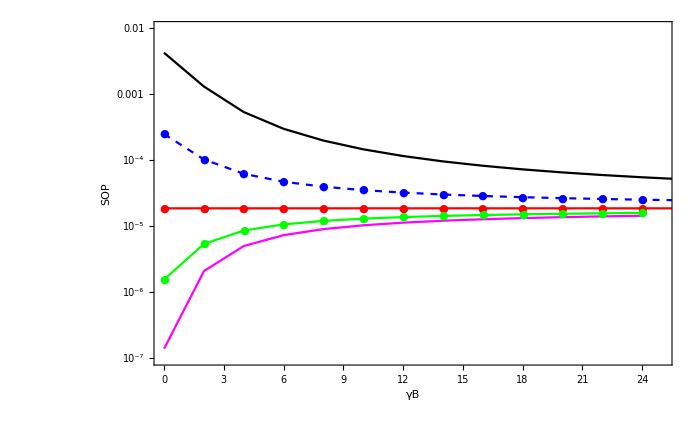

```mathematica
ListLogPlot[{plsCase1Fig6NumericalSol,plsCase2Fig6NumericalSol,plsCase3Fig6NumericalSol,plsCase4Fig6NumericalSol,plsCase5Fig6NumericalSol},PlotRange->{{0,25},{10^-7,0.01}},Joined->{True,True,True},PlotStyle->{Directive[Black],Directive[Blue,Dashed],Directive[Red],Directive[Green],Directive[Magenta],Directive[Brown]},FrameLabel->{Text[Style["γB",20]],Text[Style["SOP",20]]},LabelStyle->Directive[Black,FontSize->18],PlotMarkers-> {"","●","●","●"},PlotLegends->Placed[LineLegend[{},Joined->Automatic,LegendMarkers->Automatic,LegendFunction->"Frame",LegendMargins->{{8,8},{0.5,0.5}},LabelStyle->{FontFamily->"Times",FontSize->12}],{Right,Top}],Frame->True,AxesOrigin->{-35,0},ImageSize->700]
```

## Figura 7 (strictly positive secrecy capacity - SPSC)

### For γE=-5 dB and NA=2, NB=1, NE=2, mb=me=1 , μ=2 and κ=1.5 (Case 1-Fig 7)

#### Proposed Approach

```mathematica
μb=2;κb=1.5;mb=1;μe=2;κe=1.5;me=1;Rs=0;NA=2; NB=1; NE=2;
```

```mathematica
AbsoluteTiming[spscCase1Fig7= Table[{r,plsAnaV1SPSC[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(-5/10),NA,NB,NE]},{r,-5,15,1}]//N]
```

{0.301828,{{-5.,0.336933},{-4.,0.437517},{-3.,0.542452},{-2.,0.644434},{-1.,0.736782},{0.,0.814747},{1.,0.876175},{2.,0.921409},{3.,0.952601},{4.,0.972793},{5.,0.985101},{6.,0.992193},{7.,0.996071},{8.,0.998093},{9.,0.999104},{10.,0.999591},{11.,0.999817},{12.,0.99992},{13.,0.999966},{14.,0.999986},{15.,0.999994}}}

```mathematica
Export["spscCase1Fig7.mat",spscCase1Fig7] ;  (*Export the data to plot in MATLAB*)
```

```mathematica
Export["C:\\Users\\David\\Desktop\\SimulacionesR1\\Data\\spscCase1Fig7.mat",spscCase1Fig7] ;
```

### For γE=-5 dB and NA=2, NB=2, NE=2, mb=me=1 , μ=2 and κ=1.5 (Case 2-Fig 7)

#### Proposed Approach

```mathematica
μb=2;κb=1.5;mb=1;μe=2;κe=1.5;me=1;Rs=0;NA=2; NB=2; NE=2;
```

```mathematica
AbsoluteTiming[spscCase2Fig7= Table[{r,plsAnaV1SPSC[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(-5/10),NA,NB,NE]},{r,-5,15,1}]//N]
```

{1.10166,{{-5.,0.666667},{-4.,0.77228},{-3.,0.856781},{-2.,0.917577},{-1.,0.9568},{0.,0.979447},{1.,0.991141},{2.,0.996541},{3.,0.998775},{4.,0.999605},{5.,0.999884},{6.,0.999969},{7.,0.999992},{8.,0.999998},{9.,1.},{10.,1.},{11.,1.},{12.,1.},{13.,1.},{14.,1.},{15.,1.}}}

```mathematica
Export["spscCase2Fig7.mat",spscCase2Fig7] ;  (*Export the data to plot in MATLAB*)
```

```mathematica
Export["C:\\Users\\David\\Desktop\\SimulacionesR1\\Data\\spscCase2Fig7.mat",spscCase2Fig7] ;
```

### For γE=-5 dB and NA=2, NB=3, NE=2, mb=me=1 , μ=2 and κ=1.5 (Case 3-Fig 7)

#### Proposed Approach

```mathematica
μb=2;κb=1.501;mb=1;μe=2;κe=1.501;me=1;Rs=0;NA=2; NB=3; NE=2;
```

```mathematica
AbsoluteTiming[spscCase3Fig7= Table[{r,plsAnaV1SPSC[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(-5/10),NA,NB,NE]},{r,-5,15,1}]//N]
```

{3.17513,{{-5.,0.852055},{-4.,0.919255},{-3.,0.960959},{-2.,0.983422},{-1.,0.993861},{0.,0.998028},{1.,0.999452},{2.,0.999868},{3.,0.999973},{4.,0.999995},{5.,0.999999},{6.,1.},{7.,1.},{8.,1.},{9.,1.},{10.,1.},{11.,1.},{12.,1.},{13.,1.},{14.,1.},{15.,1.}}}

```mathematica
Export["spscCase3Fig7.mat",spscCase3Fig7] ;  (*Export the data to plot in MATLAB*)
```

```mathematica
Export["C:\\Users\\David\\Desktop\\SimulacionesR1\\Data\\spscCase3Fig7.mat",spscCase3Fig7] ;
```

### For γE=5 dB and NA=2, NB=1, NE=2, mb=me=4, μ=1 and κ=1.5 (Case 4-Fig 7)

#### Proposed Approach

```mathematica
μb=1;κb=1.5;mb=4;μe=1;κe=1.5;me=4;Rs=0;NA=2; NB=1; NE=2;
```

```mathematica
AbsoluteTiming[spscCase4Fig7= Table[{r,plsAnaV2SPSC[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(5/10),NA,NB,NE]},{r,-5,15,1}]//N]
```

{3.87694,{{-5.,0.00721267},{-4.,0.0113654},{-3.,0.0178219},{-2.,0.0277439},{-1.,0.0427449},{0.,0.0649282},{1.,0.096794},{2.,0.140917},{3.,0.199329},{4.,0.272676},{5.,0.359406},{6.,0.455431},{7.,0.55461},{8.,0.650046},{9.,0.735711},{10.,0.807707},{11.,0.864686},{12.,0.907463},{13.,0.938177},{14.,0.959442},{15.,0.973753}}}

```mathematica
Export["spscCase4Fig7.mat",spscCase4Fig7] ;  (*Export the data to plot in MATLAB*)
```

```mathematica
Export["C:\\Users\\David\\Desktop\\SimulacionesR1\\Data\\spscCase4Fig7.mat",spscCase4Fig7] ;
```

### For γE=5 dB and NA=2, NB=2, NE=2, mb=me=4, μ=1 and κ=1.5 (Case 5-Fig 7)

#### Proposed Approach

```mathematica
μb=1;κb=1.5;mb=4;μe=1;κe=1.5;me=4;Rs=0;NA=2; NB=2; NE=2;
```

```mathematica
AbsoluteTiming[spscCase5Fig7= Table[{r,plsAnaV2SPSC[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(5/10),NA,NB,NE]},{r,-5,15,1}]//N]
```

{55.0002,{{-5.,0.0208197},{-4.,0.0325283},{-3.,0.0503572},{-2.,0.0769517},{-1.,0.115525},{0.,0.169446},{1.,0.241353},{2.,0.331826},{3.,0.438004},{4.,0.552959},{5.,0.666667},{6.,0.768645},{7.,0.851178},{8.,0.91137},{9.,0.951019},{10.,0.974745},{11.,0.987755},{12.,0.994364},{13.,0.997514},{14.,0.998939},{15.,0.999558}}}

```mathematica
Export["spscCase5Fig7.mat",spscCase5Fig7] ;  (*Export the data to plot in MATLAB*)
```

```mathematica
Export["C:\\Users\\David\\Desktop\\SimulacionesR1\\Data\\spscCase5Fig7.mat",spscCase5Fig7] ;
```

### For γE=5 dB and NA=2, NB=3, NE=2, mb=me=4, μ=1 and κ=1.5 (Case 6-Fig 7)

#### Proposed Approach

```mathematica
μb=1;κb=1.5;mb=4;μe=1;κe=1.5;me=4;Rs=0;NA=2; NB=3; NE=2;
```

```mathematica
AbsoluteTiming[spscCase6Fig7= Table[{r,plsAnaV2SPSC[μb,μe,κb,κe,mb,me,Rs,10^(r/10),10^(5/10),NA,NB,NE]},{r,-5,15,1}]//N]
```

{396.248,{{-5.,0.0399556},{-4.,0.0617701},{-3.,0.0941828},{-2.,0.140906},{-1.,0.205599},{0.,0.290628},{1.,0.395313},{2.,0.514336},{3.,0.637496},{4.,0.751885},{5.,0.84609},{6.,0.914233},{7.,0.957274},{8.,0.980979},{9.,0.992399},{10.,0.99725},{11.,0.999089},{12.,0.99972},{13.,0.999919},{14.,0.999977},{15.,0.999994}}}

```mathematica
Export["spscCase6Fig7.mat",spscCase6Fig7] ;  (*Export the data to plot in MATLAB*)
```

```mathematica
Export["C:\\Users\\David\\Desktop\\SimulacionesR1\\Data\\spscCase6Fig7.mat",spscCase6Fig7] ;
```

### PLOTS OF ANALYTICAL RESULTS

```mathematica
ListPlot[{spscCase1Fig7,spscCase2Fig7,spscCase3Fig7,spscCase4Fig7,spscCase5Fig7,spscCase6Fig7},PlotRange->{{-5,15},{10^-75,1}},Joined->{True,True,True},PlotStyle->{Directive[Black],Directive[Blue,Dashed],Directive[Red],Directive[Green]},FrameLabel->{Text[Style["γB",20]],Text[Style["SPSC",20]]},LabelStyle->Directive[Black,FontSize->18],PlotMarkers-> {"","●","●","●"},PlotLegends->Placed[LineLegend[{},Joined->Automatic,LegendMarkers->Automatic,LegendFunction->"Frame",LegendMargins->{{8,8},{0.5,0.5}},LabelStyle->{FontFamily->"Times",FontSize->12}],{Left,Bottom}],Frame->True,AxesOrigin->{-35,0},ImageSize->700]
```

-Graphics-